```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# All intertwiners Immirzi 0.1

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
getfile[Dl_,K_]:=  StringJoin["../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_",ToString[Dl],"/heptapod_pcutoff_",ToString[NumberForm[N[K],{3,1}]],".csv"];
```

```mathematica
getfile[0,1/2]
```

../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/heptapod_pcutoff_0.5.csv

```mathematica
A00KDl0 = {};
A01KDl0 = {};
A11KDl0 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[0,k],"Data",HeaderLines->1];
AppendTo[A00KDl0,{k,tmp00}];
AppendTo[A01KDl0,{k,tmp01}];
AppendTo[A11KDl0,{k,tmp11}];
]
```

```mathematica
A00KDl1 = {};
A01KDl1 = {};
A11KDl1 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[1,k],"Data",HeaderLines->1];
AppendTo[A00KDl1,{k,tmp00}];
AppendTo[A01KDl1,{k,tmp01}];
AppendTo[A11KDl1,{k,tmp11}];
]
```

```mathematica
A00KDl2 = {};
A01KDl2 = {};
A11KDl2 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[2,k],"Data",HeaderLines->1];
AppendTo[A00KDl2,{k,tmp00}];
AppendTo[A01KDl2,{k,tmp01}];
AppendTo[A11KDl2,{k,tmp11}];
]
```

```mathematica
A00KDl3 = {};
A01KDl3 = {};
A11KDl3 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[3,k],"Data",HeaderLines->1];
AppendTo[A00KDl3,{k,tmp00}];
AppendTo[A01KDl3,{k,tmp01}];
AppendTo[A11KDl3,{k,tmp11}];
]
```

```mathematica
A00KDl4 = {};
A01KDl4 = {};
A11KDl4 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[4,k],"Data",HeaderLines->1];
AppendTo[A00KDl4,{k,tmp00}];
AppendTo[A01KDl4,{k,tmp01}];
AppendTo[A11KDl4,{k,tmp11}];
]
```

```mathematica
A00KDl5 = {};
A01KDl5 = {};
A11KDl5 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[5,k],"Data",HeaderLines->1];
AppendTo[A00KDl5,{k,tmp00}];
AppendTo[A01KDl5,{k,tmp01}];
AppendTo[A11KDl5,{k,tmp11}];
]
```

```mathematica
A00KDl6 = {};
A01KDl6 = {};
A11KDl6 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[6,k],"Data",HeaderLines->1];
AppendTo[A00KDl6,{k,tmp00}];
AppendTo[A01KDl6,{k,tmp01}];
AppendTo[A11KDl6,{k,tmp11}];
]
```

```mathematica
A00KDl7 = {};
A01KDl7 = {};
A11KDl7 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[7,k],"Data",HeaderLines->1];
AppendTo[A00KDl7,{k,tmp00}];
AppendTo[A01KDl7,{k,tmp01}];
AppendTo[A11KDl7,{k,tmp11}];
]
```

```mathematica
A00KDl8 = {};
A01KDl8 = {};
A11KDl8 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[8,k],"Data",HeaderLines->1];
AppendTo[A00KDl8,{k,tmp00}];
AppendTo[A01KDl8,{k,tmp01}];
AppendTo[A11KDl8,{k,tmp11}];
]
```

```mathematica
A00KDl9 = {};
A01KDl9 = {};
A11KDl9 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[9,k],"Data",HeaderLines->1];
AppendTo[A00KDl9,{k,tmp00}];
AppendTo[A01KDl9,{k,tmp01}];
AppendTo[A11KDl9,{k,tmp11}];
]
```

```mathematica
A00KDl10 = {};
A01KDl10 = {};
A11KDl10 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[10,k],"Data",HeaderLines->1];
AppendTo[A00KDl10,{k,tmp00}];
AppendTo[A01KDl10,{k,tmp01}];
AppendTo[A11KDl10,{k,tmp11}];
]
```

```mathematica
Clear[k]
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

{0.,3.68532×10^-8,1.85466×10^-7,2.17674×10^-7,2.32455×10^-7,2.40614×10^-7,2.45588×10^-7,2.4885×10^-7,2.51107×10^-7,2.52732×10^-7,2.5394×10^-7,2.5486×10^-7,2.55577×10^-7,2.56144×10^-7,2.56601×10^-7,2.56973×10^-7,2.57279×10^-7,2.57534×10^-7,2.57748×10^-7,2.57929×10^-7,2.58084×10^-7}

```mathematica
rExtrapolation00= Aitken/@Transpose[{Last/@A00KDl0,Last/@A00KDl1,Last/@A00KDl2,Last/@A00KDl3,Last/@A00KDl4,Last/@A00KDl5,Last/@A00KDl6,Last/@A00KDl7,Last/@A00KDl8,Last/@A00KDl9,Last/@A00KDl10}]
rExtrapolation01=Aitken/@Transpose[{Last/@A01KDl0,Last/@A01KDl1,Last/@A01KDl2,Last/@A01KDl3,Last/@A01KDl4,Last/@A01KDl5,Last/@A01KDl6,Last/@A01KDl7,Last/@A01KDl8,Last/@A01KDl9,Last/@A01KDl10}]
rExtrapolation11=Aitken/@Transpose[{Last/@A11KDl0,Last/@A11KDl1,Last/@A11KDl2,Last/@A11KDl3,Last/@A11KDl4,Last/@A11KDl5,Last/@A11KDl6,Last/@A11KDl7,Last/@A11KDl8,Last/@A11KDl9,Last/@A11KDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.58448×10^-8,5.71328×10^-8,5.74849×10^-8,6.78594×10^-8,7.43578×10^-8,7.8811×10^-8,8.20546×10^-8,8.45233×10^-8,8.64656×10^-8,8.80339×10^-8,8.93269×10^-8,9.04113×10^-8,9.13339×10^-8,9.21284×10^-8,9.28199×10^-8,9.34271×10^-8,9.39646×10^-8,9.44437×10^-8,9.48735×10^-8,9.52612×10^-8}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,-8.77465×10^-11,-2.23045×10^-10,3.12867×10^-8,3.06716×10^-8,3.03869×10^-8,3.0238×10^-8,3.01533×10^-8,3.01021×10^-8,3.00698×10^-8,3.00487×10^-8,3.00346×10^-8,3.0025×10^-8,3.00184×10^-8,3.00139×10^-8,3.00109×10^-8,3.00088×10^-8,3.00075×10^-8,3.00067×10^-8,3.00063×10^-8,3.00062×10^-8}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.58935×10^-8,5.67538×10^-8,9.34356×10^-8,1.03082×10^-7,1.09242×10^-7,1.13519×10^-7,1.16661×10^-7,1.19068×10^-7,1.20972×10^-7,1.22514×10^-7,1.2379×10^-7,1.24863×10^-7,1.25777×10^-7,1.26566×10^-7,1.27253×10^-7,1.27858×10^-7,1.28393×10^-7,1.28871×10^-7,1.293×10^-7,1.29688×10^-7}

```mathematica
Extrapolation00=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation00];
Extrapolation01=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation01];
Extrapolation11=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation11];
```

### Intertwiners 00

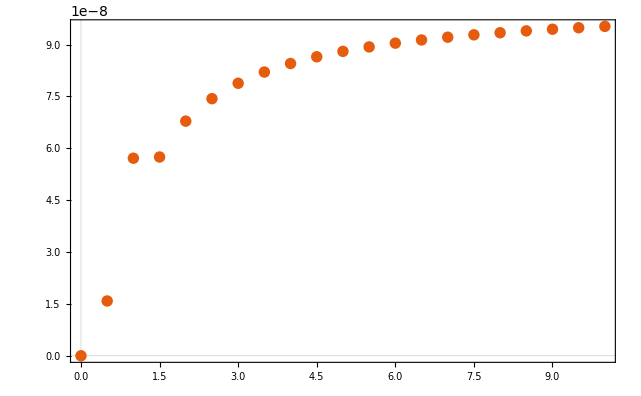

```mathematica
ListPlot[{Extrapolation00}]
```

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[1.02121×10^-7+(1.06981×10^-8)/k^2-(7.41402×10^-8)/k+1.95039×10^-10 Log[k]]

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[1.02712×10^-7+(1.22424×10^-8)/k^2-(7.58099×10^-8)/k]

```mathematica
fitExtrap00["ParameterConfidenceIntervals"]
```

{{1.02695×10^-7,1.02729×10^-7},{-7.59542×10^-8,-7.56657×10^-8},{1.19885×10^-8,1.24964×10^-8}}

```mathematica
fit1 =First/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

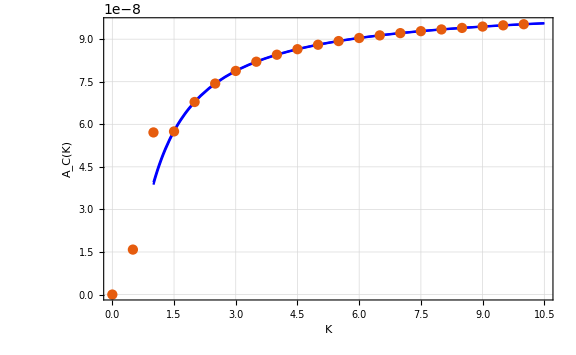

```mathematica
Show[Plot[{fit1,fit2},{k,1,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation00,PlotRange->All],PlotRange->All]
```

### Intertwiners 11

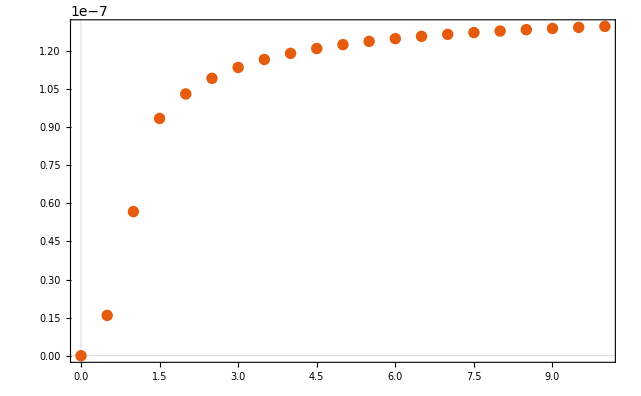

```mathematica
ListPlot[{Extrapolation11}]
```

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[1.36465×10^-7+(1.51628×10^-8)/k^2-(7.467×10^-8)/k+2.34654×10^-10 Log[k]]

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[1.37177×10^-7+(1.70208×10^-8)/k^2-(7.66789×10^-8)/k]

```mathematica
fitExtrap11["ParameterConfidenceIntervals"]
```

{{1.37156×10^-7,1.37197×10^-7},{-7.68545×10^-8,-7.65033×10^-8},{1.67117×10^-8,1.733×10^-8}}

```mathematica
fit1 =First/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

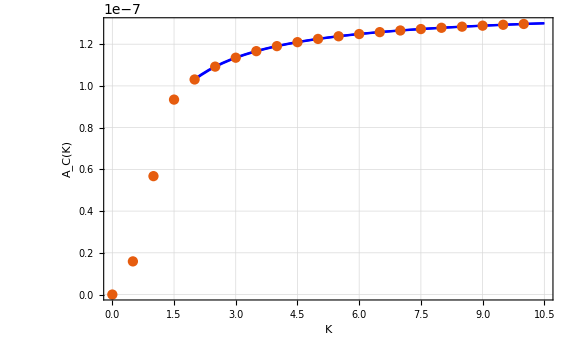

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation11,PlotRange->All],PlotRange->All]
```

### Intertwiners 01

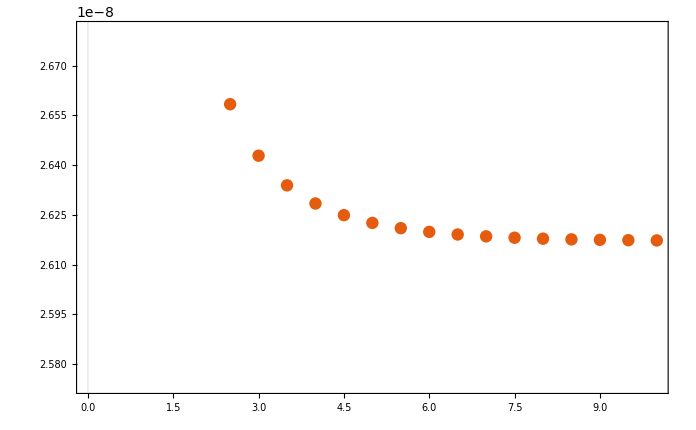

```mathematica
ListPlot[{A01KDl10}]
```

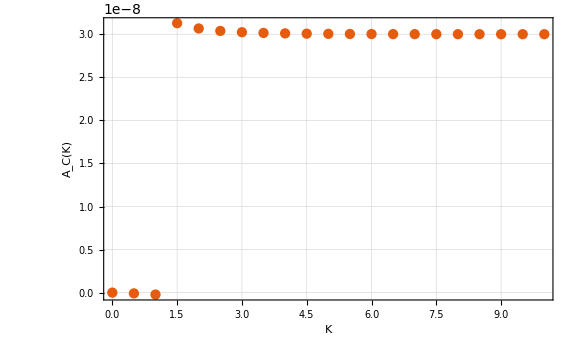

```mathematica
ListPlot[Extrapolation01,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

# Immirzi 1

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_1.0/divergence/cutoff_10.0/heptapod_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,4.71162×10^-14,1.57768×10^-13,2.0262×10^-13,2.65774×10^-13,3.16101×10^-13,3.57125×10^-13,3.91176×10^-13,4.19871×10^-13,4.44368×10^-13,4.65517×10^-13,4.83954×10^-13,5.00167×10^-13,5.14531×10^-13,5.27346×10^-13,5.38846×10^-13,5.49225×10^-13,5.58637×10^-13,5.67211×10^-13,5.75054×10^-13,5.82256×10^-13}

```mathematica
Extrapolationg1=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1,10,1/2}]&@rExtrapolation]
```

{{0,0},{1,1.57768×10^-13},{3/2,2.0262×10^-13},{2,2.65774×10^-13},{5/2,3.16101×10^-13},{3,3.57125×10^-13},{7/2,3.91176×10^-13},{4,4.19871×10^-13},{9/2,4.44368×10^-13},{5,4.65517×10^-13},{11/2,4.83954×10^-13},{6,5.00167×10^-13},{13/2,5.14531×10^-13},{7,5.27346×10^-13},{15/2,5.38846×10^-13},{8,5.49225×10^-13},{17/2,5.58637×10^-13},{9,5.67211×10^-13},{19/2,5.75054×10^-13},{10,5.82256×10^-13}}

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[5.39207×10^-13+(7.28858×10^-13)/k^2-(9.82458×10^-13)/k+5.8313×10^-14 Log[k]]

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[7.21874×10^-13+(1.3401×10^-12)/k^2-(1.54633×10^-12)/k]

```mathematica
fitExtrapg1["ParameterConfidenceIntervals"]
```

{{7.17426×10^-13,7.26322×10^-13},{-1.58948×10^-12,-1.50318×10^-12},{1.24991×10^-12,1.4303×10^-12}}

```mathematica
fit1 =First/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

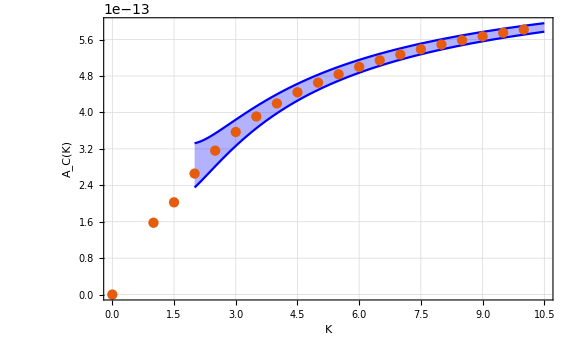

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolationg1,PlotRange->All],PlotRange->All]
```

# Immirzi 0.1 and dimension (2j+1)^2

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/divergence/cutoff_10.0/frogface_Dl_min_0_Dl_max_10_dim_2.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.49902×10^-7,1.83178×10^-6,3.73993×10^-6,5.67121×10^-6,7.8159×10^-6,0.0000101895,0.0000127974,0.0000156418,0.000018724,0.0000220455,0.0000256082,0.0000294152,0.0000334703,0.0000377783,0.0000423452,0.0000471774,0.0000522825,0.0000576686,0.0000633447,0.0000693208}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,1.49902×10^-7},{1,1.83178×10^-6},{3/2,3.73993×10^-6},{2,5.67121×10^-6},{5/2,7.8159×10^-6},{3,0.0000101895},{7/2,0.0000127974},{4,0.0000156418},{9/2,0.000018724},{5,0.0000220455},{11/2,0.0000256082},{6,0.0000294152},{13/2,0.0000334703},{7,0.0000377783},{15/2,0.0000423452},{8,0.0000471774},{17/2,0.0000522825},{9,0.0000576686},{19/2,0.0000633447},{10,0.0000693208}}

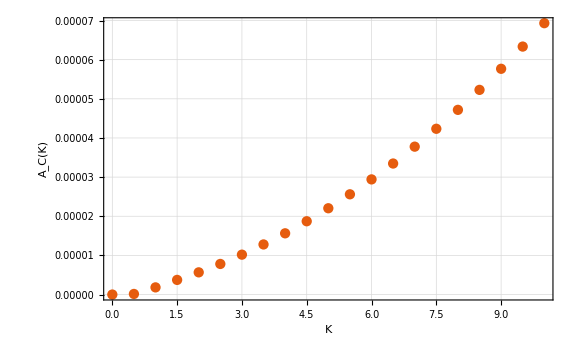

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[-8.84847×10^-7+2.45239×10^-6 k+3.96413×10^-7 k^2+6.01962×10^-9 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{-8.84847×10^-7,0.0000245239,0.0000396413,6.01962×10^-6}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→6.01962×10^-9,b→3.96413×10^-7,c→2.45239×10^-6,d→-8.84847×10^-7}